## Essentials of Mathematica: Solving ODE’s Analytically and Numerically (Optional)

## Learning Objectives:

(Optional) Learn how to solve ODE’s analytically or symbolically and display the results

(Optional) Learn how to solve ODE’s numerically and display the resultstor

Note: This lab book is mostly based on the PHYS 230 Computational Physics manual from BYU written by Dr. John S. Colton, with permission.

## Symbolic solutions to ordinary differential equations

1D projectile
Suppose that we throw a ball straight up and wish to find the position z, velocity v, and acceleration a as functions of time.  The differential equation for this situation is  
	F=m a = -m g	or	(d^2 z)/(d t^2) = -g, 
where we have taken the convention that the positive z direction is up.  

Basic usage of DSolve
We can use Mathematica’s DSolve to solve the differential equation and obtain z as a function of t.  For the function to work in the solver you need to use “==” rather than “=” when defining equations. To make the notebook easier to read I’ll name the equation to solve eqns and then put it into the function.

```mathematica
eqns = {z''[t]==-g } 
dsols = DSolve[eqns,z[t],t]
```

{z''[t]==-g}

{{z[t]→-(g t^2)/2+C[1]+t C[2]}}

Mathematica gives the solution as a double-nested list that contains a single replacement rule (the thing with the “→” in it). The inner list only contains one expression because we are only solving for one variable (i.e. z[t]).  The outer list only contains one expression because the differential equation only has one general solution.

Replacement rule solutions
We have to use the replacement rule (slash-dot) to extract the solution from the dsols list and store it in a variable with a different name (i.e. position) like this:

```mathematica
position= z[t]/.dsols[[1]]
```

-(g t^2)/2+C[1]+t C[2]

Initial Conditions
We didn't specify any initial conditions above, so the solution contained unknown constants C[1] and C[2].  To include an initial condition, we give DSolve a list of equations rather than a single equation, and include the initial conditions in the list.

```mathematica
eqns = {z''[t]==-g ,z[0]==z0,z'[0]==v0} 
dsols = DSolve[eqns,z[t],t]
position= z[t]/.dsols[[1]]//Expand
```

{z''[t]==-g,z[0]==z0,z'[0]==v0}

{{z[t]→1/2 (-g t^2+2 t v0+2 z0)}}

-(g t^2)/2+t v0+z0

Plotting the Solution
To plot the solution as a function of time we need to specify the values of the parameters g, z0, and v0.  Again, we use variable replacements rather than variable assignments to specify the values.  Here we use a list of replacement rules called testcase to specify the parameters, and then plot the position versus time for these parameters.

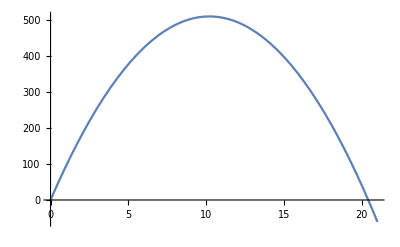

```mathematica
testcase= {g->9.8,z0->0, v0->100};
Plot[position/.testcase,{t,0,21}]
```

Evaluate the cell below, and observe that the original equations and solutions can still be viewed and utilized symbolically since we used replacements rather than assignments.

```mathematica
eqns
position
```

{z''[t]==-g,z[0]==z0,z'[0]==v0}

-(g t^2)/2+t v0+z0

Working with the solution
Now that we have z(t), we can use time derivatives to obtain the velocity v(t) and acceleration a(t) and then plot them using the set of parameters stored in testcase, like this

-g t+v0

-g

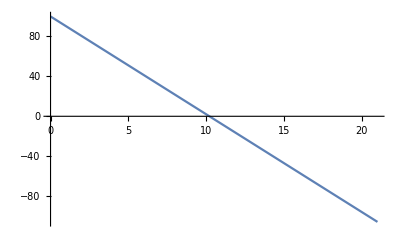

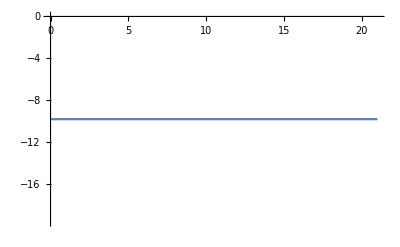

```mathematica
velocity =D[position,t]
acceleration = D[position,{t,2}]
Plot[velocity/.testcase,{t,0,21}]
Plot[acceleration/.testcase,{t,0,21}]
```

Measuring projectile quantities
Use the plots above to visually determine how long it takes the ball to return to the ground (z = 0) and its velocity upon arrival.  We can also use Mathematica to find the time it returns to the ground by using Solve, like this

```mathematica
sol = Solve[(position/.testcase)==0,t]
returntime = t/.sol[[2]]
returnvelocity = velocity/.testcase /. sol[[2]]
```

{{t→0.+0. ⅈ},{t→20.4082}}

20.4082

-100.

Look at the plots again, and determine how high the ball goes before it falls back down to the ground.  We can solve this in Mathematica like this:

```mathematica
sol = Solve[(velocity/.testcase)==0,t]
peakheight = position/.testcase/.sol[[1]]
```

{{t→10.2041}}

510.204

## Numerical solutions to ordinary differential equations

1D projectile at large distances
Let’s consider the 1D projectile again, but instead of throwing balls we’ll launch rockets.  Since the projectile doesn’t stay near the surface of the earth  we have to use the full form of Newton’s law of gravitation: 
									(d^2 z)/(d t^2) = -G M/z^2 , 
Here G is the universal gravitational constant and M is the mass of the earth.  The addition of the z^2 term in the denomiator makes this equation nonlinear and very hard to solve analytically.  DSolve just chokes now, but its cousin NDSolve can give us a numerical solution.  

Write your equation as a set of first order equations
Second order differential equations are hard to solve directly with numerical methods.  It is better to recast them as a set of first order differential equations (although you don’t have to do that as you will see later). For the projectile, we can just define the velocity v(t) explicitly as the first time derivative of z(t) to get a first order set, like this:  
							dz/(d t) = v	              	dv/(d t) = -G M/z^2
It is always possible to use this technique to change a higher order differential equation into a set of first order equations.  If you give NDSolve a higher order differential equation, it is smart enough to break it into a first-order set internally, but we’d like you to get in the habit of making the first order set explicitly.  When we add in the initial conditions, our set of equations becomes

```mathematica
eqns={z'[t]==v[t],v'[t]==-G*M/z[t]^2,v[0]==v0,z[0]==z0}
```

{z'[t]==v[t],v'[t]==-(G M)/z[t]^2,v[0]==v0,z[0]==z0}

Getting a numeric solution with NDSolve
Numeric solutions can’t have variables in them because they are just a sequence of numbers representing the function values.  So, in contrast to our approach with analytic solutions, we pick values for all our parameters at the beginning with NDSolve.  We also have to specify the range of t values over which a numeric solution will be computed, since Mathematica can’t store every possible value for our solution.

In our case, the position z now represents the distance from the center of the earth, so we use z0 = 6.4×10^6 to start our projectile from the surface of the earth.  We’ll choose an initial velocity of 8,000 m/s, which is about the speed that the Saturn V rockets achieved as they left the atmosphere.  The mass of the earth and G are known constants.  For the time range, we use {t, 0, 4700}, which is about the time it takes for our rocket to come crashing back to the earth.  If you extend the time range much farther than this, Mathematica complains because the denominator goes to zero as the rocket falls to the center of the earth.

```mathematica
testcase={M->6 10^24 ,G->6.67×10^-11, v0->8 10^3,z0->6.4 10^6}
tmin = 0; tmax =4700;
nsols = NDSolve[eqns/.testcase,{z[t],v[t]},{t,tmin,tmax}]
```

{M→6000000000000000000000000,G→6.67×10^-11,v0→8000,z0→6.4×10^6}

{{z[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t]}}

The solutions appear as nested lists of replacement rules like they did with DSolve.  However, each replacement object is now a numerical object called an InterpolatingFunction over the variable t. We dealt with these types of function when we learned how to interpolate data. An interpolating functions is essentially a table of numbers that Mathematica uses to represent a function at various values of t.

We can store the interpolating functions in a variables and plot them, like this

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

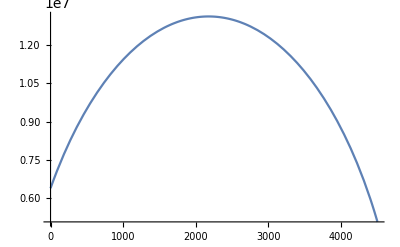

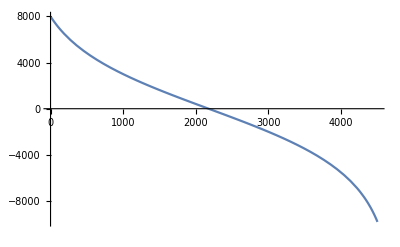

```mathematica
position= z[t]/.nsols[[1]]
velocity =v[t]/.nsols[[1]]
Plot[position,{t,0,4500}]
Plot[ velocity,{t,0,4500}]
```

Working with InterpolatingFunctions
Interpolating functions can be treated much like any other function of t.  Here is how you take the derivative of velocity to find acceleration:

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

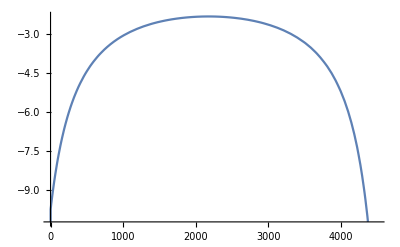

```mathematica
velocity =D[position,t]
acceleration = D[position,{t,2}]
Plot[ acceleration,{t,0,4500}]
```

Notice that the acceleration is not constant now since our projectile moves a significant distance from the surface of the earth.

We can use our interpolating functions to calculate how long it takes the rocket to fall back to the earth. Interpolating functions are inherently numeric, so we rephrase this problem as a numeric root-search operation.  Given a reasonably good initial guess, Mathematica's FindRoot function will numerically find a nearby root (a place where the function is zero).  We will use t = 4,000 as the initial guess, which we obtained visually from the z(t) graph above.

```mathematica
sol =FindRoot[position-6.4 10^6,{t,4000}]
returntime = t/.sol
returnvelocity = velocity/.sol
```

{t→4351.28}

4351.28

-8000.03

For scale, it may be helpful to recall that there are 3,600 s in an hour.  Note that the return velocity is not exactly the initial velocity because numerical solutions have an inherent amount of error.

Using a similar technique, we can determine how high the rocket went before it fell back down to the ground.  We again use FindRoot, starting with an approximate peak position obtained from the z(t) graph above.

```mathematica
sol = FindRoot[velocity,{t,2000}]
peakheight = position/.sol
```

{t→2175.64}

1.31079×10^7

For scale, it may be helpful to recall that the moon orbits at about 3.8×10^8 m.  You’ll notice that we didn’t quite achieve a moon-shot with our Saturn V.  When we really went to the moon, this first phase just got the rocket into earth orbit.  Once they were sure everything was OK in earth orbit, they did another long burn to send the rocket on an energy-efficient curved path to the moon.  We’d need to use a 2D model to simulate the actual flight path.

### Example 2: Pendulum

In physics 182 you studied the motion of a pendulum.  After drawing a free body diagram and doing a little trigonometry you should have found the following Newton’s 2nd in the rotational coordinate system:
						F_θ[t]=mα[t]=mθ''[t]=-mg/l sin(θ[t])
canceling mass gives you the following second order differential equation:
							θ''[t]=-g/l sin(θ[t])
This equation cannot be solved easily by hand, so you employed the small angle approximation to study the pendulum’s movement when started with a small angular displacement.  Under this approximation θ~sin[θ] and θ''[t]=-g/l θ[t].  This DE has an analytic solution that is easy to determine.  We’ll use DSolve to find it anyway.

```mathematica
eq1=θ''[t]==-g/l θ[t];
eq2=θ'[0]==0;
eq3=θ[0]==ϕ;
DSolve[{eq1,eq2,eq3},{θ},{t}]
```

{{θ→Function[{t},ϕ Cos[(√g t)/(√l)]]}}

However,  DSolve cannot be used to find the solution to the actual differential equation that describes the pendulum’s motion.

```mathematica
(*This will not work*)
eq1=θ''[t]==-g/l Sin[θ[t]];
eq2=θ'[0]==0;
eq3=θ[0]==ϕ;
DSolve[{eq1,eq2,eq3},{θ},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

Instead we need to make a numerical approximation of the solution to the differential equation.  You will learn how to code this up later in the course, but below shows you how it is done.  Note that the solver does not give you an analytical equation of the position of the pendulum as a solution (there isn’t one) instead it gives you an interpolated function  of the position that you can use to determine the position at a given time.

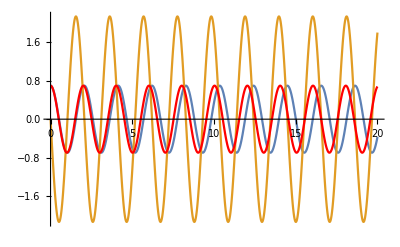

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
g=9.8;                         (*acceleration of gravity, m/s^2*)
l=1;                            (*length of pendulum, in meters*)
finaltime=20;       (*Final time of the simulation, in seconds*)  
startang=40*Pi/180;  (*The initial start angle.  Play around with this. Compare the actual solution to the approximate one*)

(*Solve the 2nd Order DE*)
eq1=y''[t]==-g/l Sin[y[t]];
eq2 = y'[0]==0;
eq3= y[0]==startang;
s=NDSolve[{eq1,eq2,eq3}, {y,y'},{t,0,finaltime}];

(*Replace rules solution with functions of angular positon and velocity*)
{theta[t_],omega[t_]}={y[t],y'[t]}/.s//Flatten;

(*Plot angular positon and velocity AND approximate solution*)
plot1=Plot[{theta[t],omega[t]},{t,0,finaltime}];
plot2=Plot[startang*Cos[Sqrt[g/l] t],{t,0,finaltime},PlotStyle->{Red}];
Show[plot1,plot2]

(*Find x,y positon for graphics*)
x[t_]=l*Sin[theta[t]];
y[t_]=-l*Cos[theta[t]];

(*Make an animation of the pendulum's motion*)
Animate[Graphics[{Disk[{x[t],y[t]},.05],Line[{{0,0},{x[t],y[t]}}]},PlotRange->{{-1.5,1.5},{-1,0}}],{t,0,finaltime},AnimationRate->.3]
```